```mathematica
l1={2299,3920,5850,8275,10602,10982,10146,7958}
```

{2299,3920,5850,8275,10602,10982,10146,7958}

```mathematica
func1=Table[{6.5+0.1i,l1[[i]]},{i,1,8}]
```

{{6.6,2299},{6.7,3920},{6.8,5850},{6.9,8275},{7.,10602},{7.1,10982},{7.2,10146},{7.3,7958}}

```mathematica
TableForm[{{"阈值/V",6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3},{"计数",2299,3920,5850,8275,10602,10982,10146,7958}}]
```

阈值/V | 6.6 | 6.7 | 6.8 | 6.9 | 7. | 7.1 | 7.2 | 7.3
计数 | 2299 | 3920 | 5850 | 8275 | 10602 | 10982 | 10146 | 7958

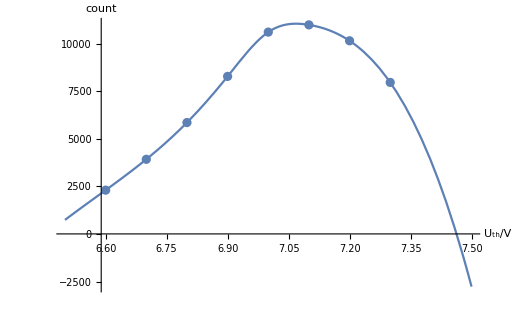

```mathematica
Show[ListPlot[func1],Plot[Interpolation[func1,Method->"Spline"][x],{x,6.5,7.5}],PlotRange->All,AxesLabel->{"U_th/V","count"}]
```

```mathematica
Maximize[Interpolation[func1,Method->"Spline"][x],x]
```

{11043.4,{x→7.0682}}

```mathematica
l2=Import["F:\\SKF\\pku\\大三上\\近代物理实验Ⅰ\\NaI(Tl)闪烁谱仪测定γ射线能谱\\skf\\cs-spectrum-data.txt","list"]
```

{93,124,341,356,1548,3438,5261,7764,10125,11072,9539,7221,5150,3370,1964,1034,464,311,272,319,313,304,390,435,524,570,793,1019,1347,1570,1831,2129,2299,2411,2361,2318,2321,2400,2245,2235,2201,2300,2182,2211,2291,2315,2310,2346,2438,2405,2477,2548,2705,2889,2909,3119,3301,3517,3541,3267,2790,2547,2422,2356,2412,2413,2317,2351,2323,2369,2447,2601,2453,2430,2438}

```mathematica
func2=Table[{8.1-0.1i,l2[[i]]},{i,1,75}]
```

{{8.,93},{7.9,124},{7.8,341},{7.7,356},{7.6,1548},{7.5,3438},{7.4,5261},{7.3,7764},{7.2,10125},{7.1,11072},{7.,9539},{6.9,7221},{6.8,5150},{6.7,3370},{6.6,1964},{6.5,1034},{6.4,464},{6.3,311},{6.2,272},{6.1,319},{6.,313},{5.9,304},{5.8,390},{5.7,435},{5.6,524},{5.5,570},{5.4,793},{5.3,1019},{5.2,1347},{5.1,1570},{5.,1831},{4.9,2129},{4.8,2299},{4.7,2411},{4.6,2361},{4.5,2318},{4.4,2321},{4.3,2400},{4.2,2245},{4.1,2235},{4.,2201},{3.9,2300},{3.8,2182},{3.7,2211},{3.6,2291},{3.5,2315},{3.4,2310},{3.3,2346},{3.2,2438},{3.1,2405},{3.,2477},{2.9,2548},{2.8,2705},{2.7,2889},{2.6,2909},{2.5,3119},{2.4,3301},{2.3,3517},{2.2,3541},{2.1,3267},{2.,2790},{1.9,2547},{1.8,2422},{1.7,2356},{1.6,2412},{1.5,2413},{1.4,2317},{1.3,2351},{1.2,2323},{1.1,2369},{1.,2447},{0.9,2601},{0.8,2453},{0.7,2430},{0.6,2438}}

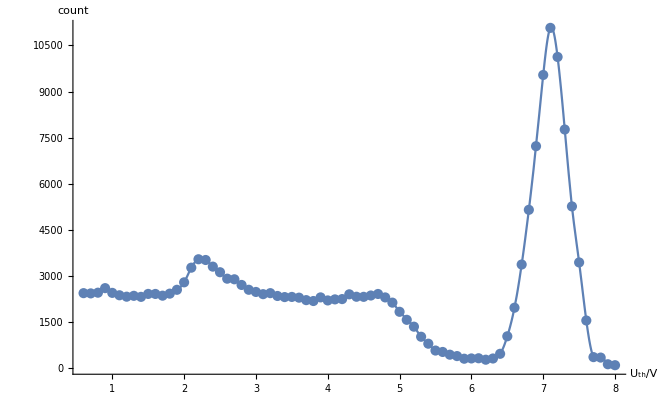

```mathematica
Show[ListPlot[func2],Plot[Interpolation[func2,Method->"Spline"][x],{x,0.6,8},PlotRange->Full],PlotRange->All,AxesLabel->{"U_th/V","count"}]
```

```mathematica
Flatten[Table[Transpose[Table[{SetAccuracy[8.1-0.1i,2],l2[[i]]},{i,10j+1,10j+10}]//Prepend[{"U_th/V","count"}]],{j,0,6}]//Append[Transpose[Table[{SetAccuracy[8.1-0.1i,2],l2[[i]]},{i,71,75}]//Prepend[{"U_th/V","count"}]]],1]//TableForm
```

U_th/V | 8. | 7.9 | 7.8 | 7.7 | 7.6 | 7.5 | 7.4 | 7.3 | 7.2 | 7.1
count | 93 | 124 | 341 | 356 | 1548 | 3438 | 5261 | 7764 | 10125 | 11072
U_th/V | 7. | 6.9 | 6.8 | 6.7 | 6.6 | 6.5 | 6.4 | 6.3 | 6.2 | 6.1
count | 9539 | 7221 | 5150 | 3370 | 1964 | 1034 | 464 | 311 | 272 | 319
U_th/V | 6. | 5.9 | 5.8 | 5.7 | 5.6 | 5.5 | 5.4 | 5.3 | 5.2 | 5.1
count | 313 | 304 | 390 | 435 | 524 | 570 | 793 | 1019 | 1347 | 1570
U_th/V | 5. | 4.9 | 4.8 | 4.7 | 4.6 | 4.5 | 4.4 | 4.3 | 4.2 | 4.1
count | 1831 | 2129 | 2299 | 2411 | 2361 | 2318 | 2321 | 2400 | 2245 | 2235
U_th/V | 4. | 3.9 | 3.8 | 3.7 | 3.6 | 3.5 | 3.4 | 3.3 | 3.2 | 3.1
count | 2201 | 2300 | 2182 | 2211 | 2291 | 2315 | 2310 | 2346 | 2438 | 2405
U_th/V | 3. | 2.9 | 2.8 | 2.7 | 2.6 | 2.5 | 2.4 | 2.3 | 2.2 | 2.1
count | 2477 | 2548 | 2705 | 2889 | 2909 | 3119 | 3301 | 3517 | 3541 | 3267
U_th/V | 2. | 1.9 | 1.8 | 1.7 | 1.6 | 1.5 | 1.4 | 1.3 | 1.2 | 1.1
count | 2790 | 2547 | 2422 | 2356 | 2412 | 2413 | 2317 | 2351 | 2323 | 2369
U_th/V | 1. | 0.9 | 0.8 | 0.7 | 0.6 |  |  |  |  | 
count | 2447 | 2601 | 2453 | 2430 | 2438 |  |  |  |  |

```mathematica
Maximize[{Interpolation[func2,Method->"Spline"][x],x≥6&&x≤8},x]
```

{11092.,{x→7.11128}}

```mathematica
func20=Interpolation[func2,Method->"Spline"]
```

InterpolatingFunction[{{0.6, 8.}}, <>]

```mathematica
MaxValue[{func20[x],x≥6&&x≤8},x]/2
```

5545.99

```mathematica
FindRoot[func20[x]==5545.99,{x,7.0}]
```

{x→6.82035}

```mathematica
l3=Import["F:\\SKF\\pku\\大三上\\近代物理实验Ⅰ\\NaI(Tl)闪烁谱仪测定γ射线能谱\\skf\\cs-co-peak-data.txt","list"]
```

{4658,4994,5419,6629,6253,5665,2556,6280,15113,19979,18304,9731,8588,8488,8904,11730,15044,20474,22012,18971,11618,6221,6212,9261,12932,16575,16434,11946,6605}

```mathematica
func3={{Table[0.8+0.1i,{i,0,5}],Table[3.3+0.1i,{i,0,5}],Table[5.8+0.1i,{i,0,16}]}//Flatten,l3}//Transpose
```

{{0.8,4658},{0.9,4994},{1.,5419},{1.1,6629},{1.2,6253},{1.3,5665},{3.3,2556},{3.4,6280},{3.5,15113},{3.6,19979},{3.7,18304},{3.8,9731},{5.8,8588},{5.9,8488},{6.,8904},{6.1,11730},{6.2,15044},{6.3,20474},{6.4,22012},{6.5,18971},{6.6,11618},{6.7,6221},{6.8,6212},{6.9,9261},{7.,12932},{7.1,16575},{7.2,16434},{7.3,11946},{7.4,6605}}

```mathematica
Grid[Flatten[{func3[[1;;10]]//Prepend[{"U_th/V","count"}]//Transpose,func3[[11;;20]]//Prepend[{"U_th/V","count"}]//Transpose,func3[[21;;29]]//Prepend[{"U_th/V","count"}]//Transpose},1],Frame->All]
```

U_th/V | 0.8 | 0.9 | 1. | 1.1 | 1.2 | 1.3 | 3.3 | 3.4 | 3.5 | 3.6
count | 4658 | 4994 | 5419 | 6629 | 6253 | 5665 | 2556 | 6280 | 15113 | 19979
U_th/V | 3.7 | 3.8 | 5.8 | 5.9 | 6. | 6.1 | 6.2 | 6.3 | 6.4 | 6.5
count | 18304 | 9731 | 8588 | 8488 | 8904 | 11730 | 15044 | 20474 | 22012 | 18971
U_th/V | 6.6 | 6.7 | 6.8 | 6.9 | 7. | 7.1 | 7.2 | 7.3 | 7.4 | 
count | 11618 | 6221 | 6212 | 9261 | 12932 | 16575 | 16434 | 11946 | 6605 |

```mathematica
l4={{1.1,0.184},{3.6,0.662},{6.4,1.17},{7.1,1.33}}
```

{{1.1,0.184},{3.6,0.662},{6.4,1.17},{7.1,1.33}}

```mathematica
LinearModelFit[l4,x,x]
```

FittedModel[-0.0227154+0.188839 x]

```mathematica
%144["AdjustedRSquared"]//Sqrt
```

0.999612

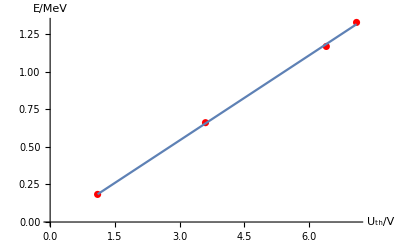

```mathematica
Show[ListPlot[l4,PlotStyle->Red],Plot[%144[x],{x,1.1,7.1}],AxesLabel->{"U_th/V","E/MeV"}]
```

```mathematica
l5=Import["F:\\SKF\\pku\\大三上\\近代物理实验Ⅰ\\NaI(Tl)闪烁谱仪测定γ射线能谱\\skf\\cs-up.dat.txt","list"];l6=Import["F:\\SKF\\pku\\大三上\\近代物理实验Ⅰ\\NaI(Tl)闪烁谱仪测定γ射线能谱\\skf\\cs-down.dat.txt","list"];
l7=Import["F:\\SKF\\pku\\大三上\\近代物理实验Ⅰ\\NaI(Tl)闪烁谱仪测定γ射线能谱\\skf\\co-down.dat.txt","list"];l8=Import["F:\\SKF\\pku\\大三上\\近代物理实验Ⅰ\\NaI(Tl)闪烁谱仪测定γ射线能谱\\skf\\cs-co-down.dat.txt","list"];
```

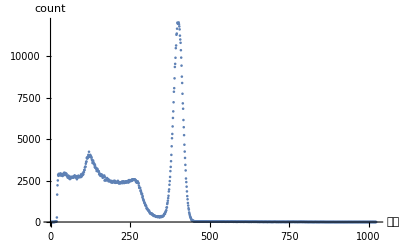

```mathematica
ListPlot[l5,PlotRange->All,AxesLabel->{"道数","count"}]
```

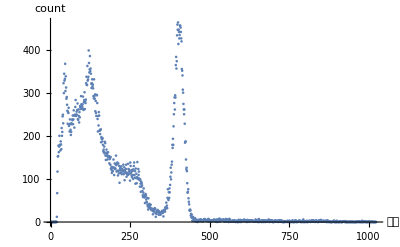

```mathematica
ListPlot[l6,AxesLabel->{"道数","count"}]
```

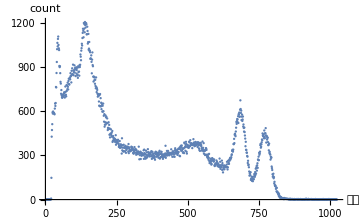

```mathematica
ListPlot[l7,AxesLabel->{"道数","count"}]
```

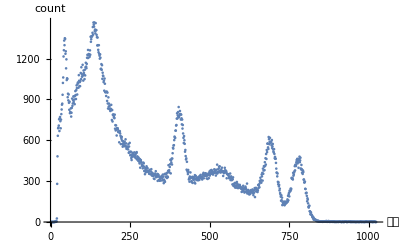

```mathematica
ListPlot[l8,AxesLabel->{"道数","count"}]
```

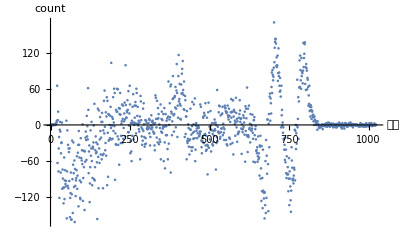

```mathematica
ListPlot[l8-l7-l6,AxesLabel->{"道数","count"}]
```

```mathematica
l9={{125,0.184},{400,0.662},{690,1.17},{770,1.33}}
```

{{125,0.184},{400,0.662},{690,1.17},{770,1.33}}

```mathematica
LinearModelFit[l9,x,x]
```

FittedModel[-0.0405449+0.00176734 x]

```mathematica
%214["AdjustedRSquared"]//Sqrt
```

0.99981

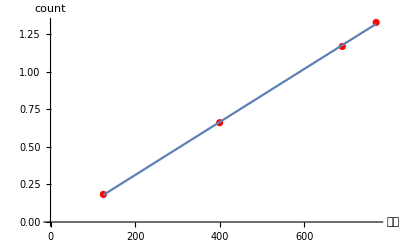

```mathematica
Show[ListPlot[l9,PlotStyle->Red],Plot[%214[x],{x,125,770}],AxesLabel->{"道数","count"}]
```

```mathematica
l9/l4
```

{{113.636,1.},{111.111,1.},{107.813,1.},{108.451,1.}}